```mathematica
NN=100; (*Размер сетки по X*)
MM=100;(*Размер сетки по T*)
UX=Array[0&,NN];
eps = 0.00001; (*Точность метода*)
ep=eps+1;
xmax= 1;xmin=0;
tmax=2; tmin=0;
U=Array[0&,{NN,MM}] ;(*Сетка*)
F[U_]:=-E^(-U^2 );(*пространственная часть уравнения переноса*)
f[U_,n_,m_]:=(*неявное уравнение f(z)==0*)
(U[[n,m-1]]-U[[n-1,m-1]]+U[[n,m]]-U[[n-1,m]])/(2*dt)+(F[U[[n,m]]]-F[U[[n,m-1]]]+F[U[[n-1,m]]]-F[U[[n-1,m-1]]])/(2*dx);
dF[U_,n_,m_]:=1/(2*dt)+2*U[[n,m]]*Exp[-U[[n,m]]^2]/(2*dx);

dx=(xmax-xmin)/(NN-1); (*Шаг сетки по X*)
dt=(tmax-tmin)/(MM-1); (*Шаг сетки по T*)
xx[i_]:=dx*i+xmin;
tt[i_]:=dt*i+tmin;
x=Array[xx,NN,0];
t=Array[tt,MM,0];
For[n=1,n<=NN,n++,
U[[1, n]]=N[Sin[Pi*x[[n]]/2]] ];(*Начальное условие на сетке*)
For[m=1,m<=MM,m++,
U[[m, 1]]=0.]; (*Граничное условие на сетке*)
dF[U,2,2]
```

99/4

```mathematica
(*Метод Ньютона*)
For[n=1,n<NN,n++,
For[m=1,m<MM,m++,
{ ep=eps+1,
While[Abs[ep]>eps, 
{ep=f[U,n+1,m+1]/dF[U,n+1,m+1],
U[[n+1,m+1]]=U[[n+1,m+1]]-ep};
]};]]
(*Конец Метода Ньютона*)

ListPlot3D[U, DataRange->{{0,1},{0,1}},AxesLabel->{X,T}]
```

-Graphics3D-

```mathematica
(*Характеристики*)
CharX[x_,x0_]:=(x-x0)/(2*Sin[Pi*x0/2])/Exp[-Sin[Pi*x0/2]^2];
(*Второй набор характерис x=const=0*)
```

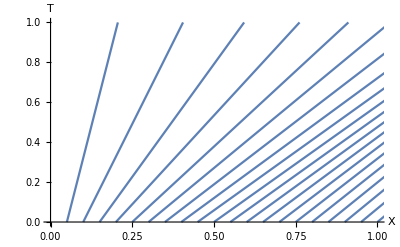

```mathematica
Plot[Table[CharX[x,x0],{x0,0.05,3.1,0.05}],{x,0,3}, PlotRange->{{0,1},{0,1}}, AxesLabel->{X,T}]
```

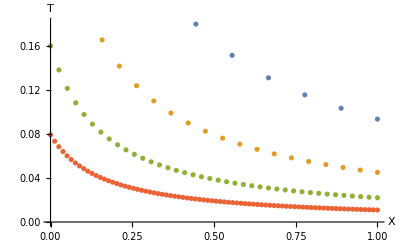

```mathematica
CountData[NN_,MM_]:=Module[{},(
eps = 0.00001; (*Точность метода*)
ep=eps+1;
xmax= 1;xmin=0;
tmax=2; tmin=0;
U=Array[0&,{NN,MM}] ;(*Сетка*)
F[U_]:=-E^(-U^2 );(*пространственная часть уравнения переноса*)
f[U_,n_,m_]:=(*неявное уравнение f(z)==0*)
(U[[n,m-1]]-U[[n-1,m-1]]+U[[n,m]]-U[[n-1,m]])/(2*dt)+(F[U[[n,m]]]-F[U[[n,m-1]]]+F[U[[n-1,m]]]-F[U[[n-1,m-1]]])/(2*dx);
dF[U_,n_,m_]:=1/(2*dt)+2*U[[n,m]]*Exp[-U[[n,m]]^2]/(2*dx);

dx=(xmax-xmin)/(NN-1); (*Шаг сетки по X*)
dt=(tmax-tmin)/(MM-1); (*Шаг сетки по T*)
xx[i_]:=dx*i+xmin;
tt[i_]:=dt*i+tmin;
x=Array[xx,NN,0];
t=Array[tt,MM,0];
For[n=1,n<=NN,n++,
U[[1, n]]=N[Sin[Pi*x[[n]]/2]] ];(*Начальное условие на сетке*)
For[m=1,m<=MM,m++,
U[[m, 1]]=0.]; (*Граничное условие на сетке*)
For[n=1,n<NN,n++,
For[m=1,m<MM,m++,
{ ep=eps+1,
While[Abs[ep]>eps, 
{ep=f[U,n+1,m+1]/dF[U,n+1,m+1],
U[[n+1,m+1]]=U[[n+1,m+1]]-ep};
]};]];
Ux[x1_]:=Module[{},(
UX=Array[0&,NN];
For[q=1,q<=NN,q++,
UX[[q]]=U[[q,x1(*/(xmax-xmin)*(NN-1)*)]]
];
Return[UX]
)];
Return[Ux[5]]
(*Конец Метода Ньютона*)
)];

ListPlot[{CountData[10,10],CountData[20,20],CountData[40,40],CountData[80,80]},DataRange->{0,1},AxesLabel->{X,T}]
```